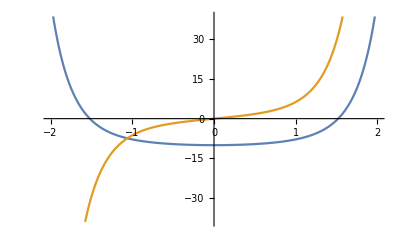

```mathematica
Plot[{Exp[x^2]-Cos[x]-10, (2 x Exp[x^2])+Sin[x]},{x, -2, 2}]
```

```mathematica
Newton's Method
```

```mathematica
f[i_]:=N[f[i-1]-(Exp[f[i-1]^2]-Cos[f[i-1]]-10)/((2 f[i-1] Exp[f[i-1]^2])+Sin[f[i-1]])];f[0]=0.2;i=1;While[  i<10,Print[{i,N[f[i],5], N[Abs[1.52-f[i]],5]}]; i++]
```

{1,16.3616,14.8416}

{2,16.331,14.811}

{3,16.3004,14.7804}

{4,16.2697,14.7497}

{5,16.239,14.719}

{6,16.2082,14.6882}

{7,16.1773,14.6573}

{8,16.1464,14.6264}

{9,16.1155,14.5955}

Investigation 2

Consider the  Newton's Method. Set the actual root,α, of the function to 1.52.
1. Table of values for f[0]=0.2  that include i ,f[i],   and  |α-f[i]|for i=1 to 9. State your observation of the values.

The table above contains values of i, f[i], and |α -f[i]| in three different columns respectively. The instructions state to print the values for i from 1 to 9, which is due to having 0.2 as the initial starting point. Based on the graph, we can see that the tangent line at 0.2 is almost completely horizontal. Because of this, we can expect the tangent line to intersect the x-axis much further down the graph. This is confirmed by the first row in the table since it shows 16.3616 as the first intersection on the x-axis. This shows the issue with Newton’s Method when choosing the starting point because a point with a horizontal tangent line goes really far from the target root. If an upper-bound error were to be chosen instead, the computer may never reach it. Therefore, we should stop at a set value of i, in this case 9, in order to avoid this problem due to the chosen starting point. 
	The values of f[i] in the table first begin at 16.3616 and slowly begin to decrease. This is because the x-intercept is slowly reaching the targeted root. Since the initial tangent line crossed the x-axis very far away, the tangent lines in that part of the graph also become much steeper, which slows the process down even more. By the ninth iteration, the x-intercept is barely at 16.1155, which is very far from the set root of 1.52. Due to the tangent line intersecting the x-axis much further down the graph, the error is also very high. The error starts off at 14.8416 and very slowly decreases to 14.5955 by the ninth iteration. Although the error is decreasing, it is doing so at a very slow pace that makes it impossible to reach an approximation of the root. This demonstrates that we cannot reach the upper-bound error of 10^-2, and that we will not have a converging sequence with an initial point of 0.2.